```mathematica
Clear[Evaluate[Context[]<>"*"]]
```

```mathematica
SetDirectory@NotebookDirectory[];
omarker=Graphics[{Thickness[.2],Disk[]}];
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListPlot]))/.Directive[x_,__]:>x)
colorsDefault=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Default",ListPlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

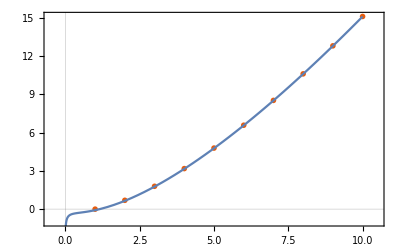

```mathematica
" Stirling approximation: effectiveness ";
Show[ListPlot[Log[Range[10]!],
PlotRange->{{-.5,10.5},{-1,All}},
PlotTheme->"Scientific",
PlotMarkers->{omarker,.03}],
Plot[x Log[x]-x+1/2 Log[2π x],{x,0,10}]]
```

```mathematica
$Assumptions={k>1};
sumApprox[k_]=∫_(3/2)^(k+1/2) x Log[x]ⅆx
```

1/8 (4-9 Log[3]-2 k (1+k) (1+Log[4])+Log[256]+(1+2 k)^2 Log[1+2 k])

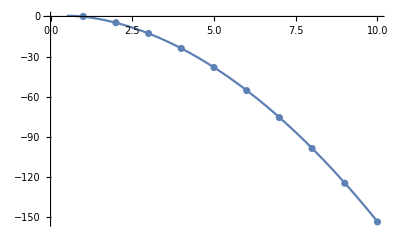

```mathematica
" Approximation by integration: effectiveness ";
Show[ListPlot[(4.∑_(m=1)^(#-1) m Log[m]-1.∑_(m=1)^(2#-1) m Log[m])&/@Range[10]],
Plot[4sumApprox[x-1]-sumApprox[2x-1],{x,0,10}]]
```

```mathematica
sumApproxMain[k_]=1/8 (-2 k (1+k) (1+Log[4])+(1+2 k)^2 Log[1+2 k]);
totalMain[x_]=4sumApproxMain[x-1]-sumApproxMain[2x-1]+x Log[2π];
asymptoticPlot=Module[{range={0,10}},
Show[Plot[
{4sumApprox[x-1]-sumApprox[2x-1]
+(2x-1)Log[x-1]-(x-1/4)Log[2x-1]
+(x-9/4)Log[2π]+3/2,
-2 x^2 Log[2]},Prepend[range,x],
PlotLabels->{"Nice","Rough"},
Epilog->{
colorsDefault⟦1⟧,
Thickness[.005],
Dashing[{Medium,Medium}],
Line[{{1,-18},{1,-140}}]
}],
ListPlot[{#,(4.∑_(m=1)^(#-1) Log[m!]-1.∑_(m=1)^(2#-1) Log[m!])}&/@Range@@range,
PlotStyle->colors⟦4⟧],
PlotRange->All,
ImageSize->360,
ImagePadding->{{24,48},{12,16}}]
]
Export@@{ToString[#]<>".pdf",ReleaseHold[#]}&@HoldForm@asymptoticPlot
```

-Graphics-

asymptoticPlot.pdf

```mathematica
SystemOpen["asymptoticPlot.pdf"]
```

```mathematica
" Nice asymptotic: very nice indeed! ";
(4.∑_(m=1)^(#-1) Log[m!]-1.∑_(m=1)^(2#-1) Log[m!])/((4sumApprox[x-1]-sumApprox[2x-1]
+(2x-1)Log[x-1]-(x-1/4)Log[2x-1]
+(x-9/4)Log[2π]+3/2)/.{x->#})&@2000//N
```

0.999999

```mathematica
" Analytic result: cool! ";
(4∑_(m=1)^(x-1) Log[m!]-∑_(m=1)^(2x-1) Log[m!])
```

4 Log[BarnesG[1+x]]-Log[BarnesG[1+2 x]]

```mathematica
4. Log[BarnesG[1.+x]]-Log[BarnesG[1.+2. x]]/.{x->10000.}
```

-1.38611×10^8